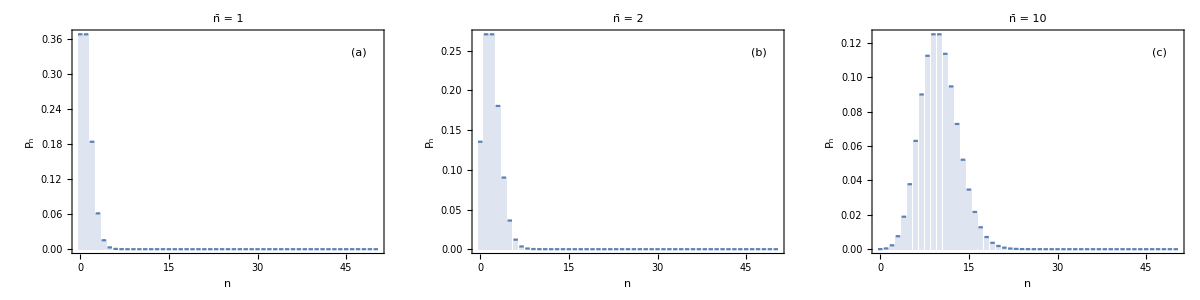

```mathematica
SetDirectory[NotebookDirectory[]];

p = PoissonDistribution[nb];

grid@Table[
DiscretePlot[PDF[p/.nb->nbb,n],{n,0,50},PlotMarkers->None,
(*PlotRange->{{-0.5,50.5},All},*)
PlotRange->All,
PlotRangePadding->{{Scaled[0.02],0},{0.0005,Scaled[0.1]}},
ExtentSize->0.75,
PlotLabel->Style["n̄ = " <> ToString@nbb,Black],
FrameLabel->{"n","P_n"}
],
{nbb,{1,2,10}}]
Export["coherent_states.png",%,ImageResolution->150];
```